Lab 1

[Your Name]

Calculations

```mathematica
Remove["Global`*"]
```

Mathematica allows you do simple calculations:

```mathematica
2+2
```

4

```mathematica
E^(Pi *I)
```

-1

It also allows you to take derivatives

```mathematica
D[E^(4x), x]
```

4 ⅇ^(4 x)

and integrals

```mathematica
Integrate[1/x, x]
Integrate[Sin[ζ*x], x]
```

Log[x]

-Cos[x ζ]/ζ

Variables

```mathematica
b=4; c=2;
5+b*c
```

13

Substitutions

```mathematica
expression1= x+2y
```

x+2 y

```mathematica
expression1/.{x->1, y->2}
```

5

Plotting

```mathematica
f=m*x+b
```

b+m x

```mathematica
f/.{m->2, b->5}
```

5+2 x

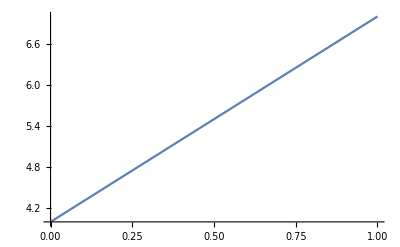

```mathematica
Plot[f/.{m->3, b->4}, {x, 0, 1}]
```

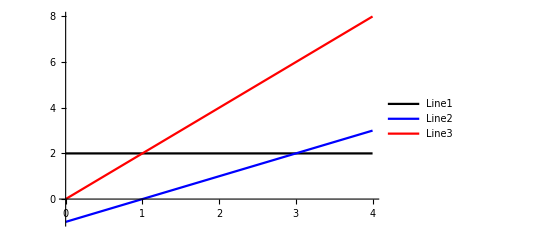

```mathematica
line1 = f/.{m->0, b->2};
line2 = f/.{m->1, b->-1};
line3=f/.{m->2, b->0};

Plot[{line1, line2, line3},
{x,0,4},
PlotStyle->{Black,Blue,Red},
PlotLegends->{Line1,Line2,Line3}]
```